```mathematica
(*This notebook creates the figures for the cjSOE model using ctDiscrete code*)
```

```mathematica
ClearAll["Global`*"];ParamsAreSet=False;
(* If running from the Notebook interface *)
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];

If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];(* root directory is above CoreCode *)
FigsDir=SetDirectory[rootDir<>"/Examples/cjSOE/Figures/"];
CodeDir=SetDirectory[rootDir<>"/Examples/cjSOE"];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
Get[CoreCodeDir<>"/ParametersBase.m"];
```

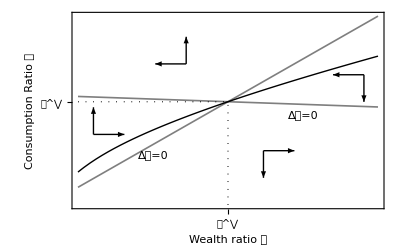

```mathematica
Get[CodeDir<>"/phaseDiagMake.m"];phaseDiagMake;Print[phaseDiag];
```

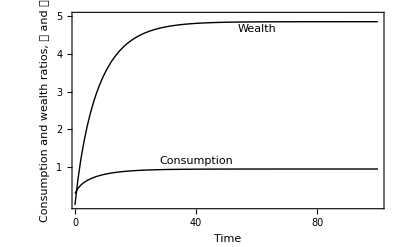

```mathematica
Get[CodeDir<>"/pathsMake.m"];pathsMake;Print[paths];
```

```mathematica
Get[CodeDir<>"/FuncsInit.m"];
Get[CodeDir<>"/FuncsSOE.m"];
Get[CodeDir<>"/FuncsIndivProblem.m"];
resetParams;
calculateValues;
```

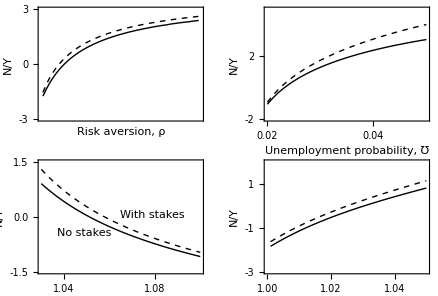

```mathematica
Get[CodeDir<>"/sensitivityMake.m"];sensitivityMake;Print[sensitivity];
```

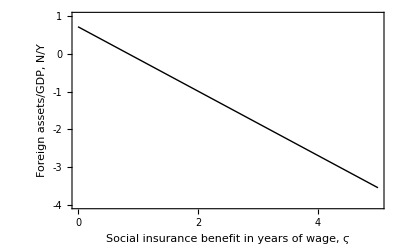

```mathematica
Get[CodeDir<>"/socInsMake.m"];socInsMake;Print[socIns];
```

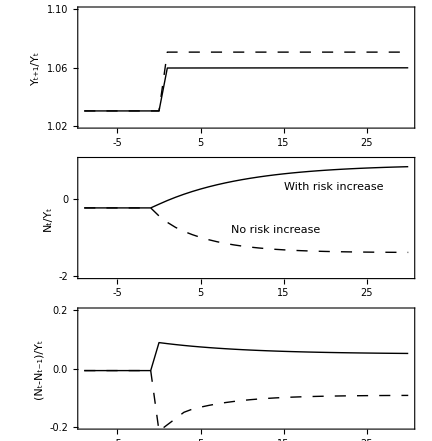

```mathematica
Get[CodeDir<>"/transDynMake.m"];transDynMake;Print[transDyn];
```

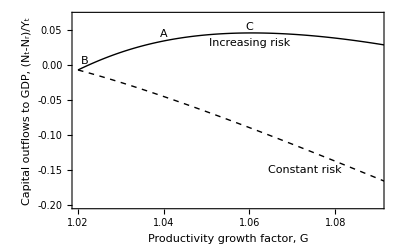

```mathematica
Get[CodeDir<>"/capOutflowsMake.m"];capOutflowsMake;Print[capOutflows];
```

```mathematica
ClearAll["Global`*"];ParamsAreSet=False;
(* If running from the Notebook interface *)
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];

If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];(* root directory is above CoreCode *)
FigsDir=SetDirectory[rootDir<>"/Examples/cjSOE/Figures/"];
CodeDir=SetDirectory[rootDir<>"/Examples/cjSOE"];
cjSOEDirCode=SetDirectory[rootDir<>"/Examples/cjSOE"];cjSOEDirFigs=SetDirectory[rootDir<>"/Examples/cjSOE/Figures"];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
Get[CoreCodeDir<>"/ParametersBase.m"];
Get[CodeDir<>"/FuncsInit.m"];
Get[CodeDir<>"/FuncsSOE.m"];
Get[CodeDir<>"/FuncsIndivProblem.m"];
resetParams;
calculateValues;
```

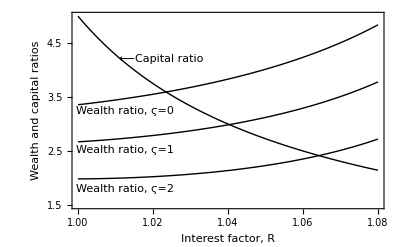

```mathematica
Get[CodeDir<>"/genEqbmMake.m"];genEqbmMake;Print[genEqbm];
```

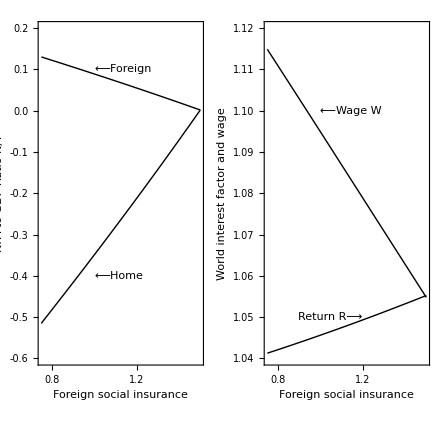

```mathematica
Get[CodeDir<>"/globImbMake.m"];globImbMake;Print[globImb];
```